```mathematica
Rutinas SSA
ScreeSSA[Serie_,L_]:=(
X=Partition[Serie,L,1];
r=MatrixRank[X];
σ=SingularValueList[N[X],r];
λ=σ^2;
λFrac=λ/Total[λ];
λLog=Table[{Log10[k]//N,Log10[λ[[k]]]//N},{k,1,r}];
λFracLog=Table[{Log10[k]//N,Log10[λFrac[[k]]]//N},{k,1,r}];
;)

PartialScreeSSA[Serie_,L_,rMax_]:=(
X=Partition[Serie,L,1];
Σ=SingularValueList[N[X],rMax][[2]];
σ=Table[Σ[[k,k]],{k,1,rMax}];
λ=σ^2;
λFrac=λ/Total[λ];
λLog=Table[{Log10[k]//N,Log10[λ[[k]]]//N},{k,1,r}];
λFracLog=Table[{Log10[k]//N,Log10[λFrac[[k]]]//N},{k,1,r}];
;)

CompleteSSA[Serie_,L_]:=(
Dim=Dimensions[Serie][[1]];
(* SVD *)
X=Partition[Serie,L,1];
K=Dimensions[X][[1]];
r=MatrixRank[X];
{U,Σ,V}=SingularValueDecomposition[N[X],r];
(* scree diagram *)
σ=Table[Σ[[k,k]],{k,1,r}];
λ=σ^2;
λFrac=λ/Total[λ];
λLog=Table[{Log10[k]//N,Log10[λ[[k]]]//N},{k,1,r}];
λFracLog=Table[{Log10[k]//N,Log10[λFrac[[k]]]//N},{k,1,r}];
(* matrices elementales *)
For[k=1,k≤r,k++,{
XX[k]=σ[[k]]*Outer[Times,Transpose[U][[k]],Transpose[V][[k]]]; 
XXX[k]=Transpose[Table[XX[k][[All,n]],{n,L,1,-1}]]
}];
(* Modos reconstruidos *)
For[k=1,k≤r,k++,{
g[k]=Table[
Mean[Diagonal[XXX[k],i]]
,{i,Min[K-1,L-1],-Max[K-1,L-1],-1}]
}];
(* wMatriz *)
w={};
LL=Min[L,K];
KK=Max[L,K];
For[i=1,i≤LL,i++,{
AppendTo[w,i]
}]
For[i=LL+1,i≤KK,i++,{
AppendTo[w,LL]
}]
For[i=KK+1,i≤Dim,i++,{
AppendTo[w,Dim-i]
}];
kMin=kkMin=1;kMax=kkMax=20;
wMatriz=Table[Total[w*g[k]*g[kk]]/(Sqrt[Total[w*g[k]^2]]*Sqrt[Total[w*g[kk]^2]]),{k,kMin,kMax},{kk,kkMin,kkMax}];
;)

PartialSSA[Serie_,L_,rMax_,gYesNo_,wYesNo_]:=(
Dim=Dimensions[Serie][[1]];
(* SVD *)
X=Partition[Serie,L,1];
K=Dimensions[X][[1]];
r=MatrixRank[X];
{U,Σ,V}=SingularValueDecomposition[N[X],rMax];
(* scree diagram *)
σ=Table[Σ[[k,k]],{k,1,rMax}];
λ=σ^2;
λFrac=λ/Total[λ];
λLog=Table[{Log10[k]//N,Log10[λ[[k]]]//N},{k,1,r}];
λFracLog=Table[{Log10[k]//N,Log10[λFrac[[k]]]//N},{k,1,r}];
If[gYesNo=="Yes",{
(* matrices elementales *)
For[k=1,k≤rMax,k++,{
XX[k]=σ[[k]]*Outer[Times,Transpose[U][[k]],Transpose[V][[k]]]; 
XXX[k]=Transpose[Table[XX[k][[All,n]],{n,L,1,-1}]]
}];
(* Modos reconstruidos *)
For[k=1,k≤rMax,k++,{
g[k]=Table[
Mean[Diagonal[XXX[k],i]]
,{i,Min[K-1,L-1],-Max[K-1,L-1],-1}]
}];
}];
If[wYesNo=="Yes",{
(* wMatriz *)
w={};
LL=Min[L,K];
KK=Max[L,K];
For[i=1,i≤LL,i++,{
AppendTo[w,i]
}]
For[i=LL+1,i≤KK,i++,{
AppendTo[w,LL]
}]
For[i=KK+1,i≤Dim,i++,{
AppendTo[w,Dim-i]
}];
kMin=kkMin=1;kMax=kkMax=Min[20,rMax];
wMatriz=Table[Total[w*g[k]*g[kk]]/(Sqrt[Total[w*g[k]^2]]*Sqrt[Total[w*g[kk]^2]]),{k,kMin,kMax},{kk,kkMin,kkMax}];
}]
;)

SetDirectory["C:\Users\sqrf\Documents\Carbono Negro"]
Semana = 1

Dat=Import["2015-CCA-CO(by weeks).xlsx",{"Data",1,All, Semana+1}];
Datos =Transpose[Table[Dat, {1}]]
(*{"Data",# of sheet(s),# of row(s),# of column(s)}
*)
{M,T}=Dimensions[Datos]
```

Rutinas SSA

C:\Users\sqrf\Documents\Carbono Negro

1

{{1.7},{1.1},{0.8},{1.1},{0.8},{2.1},{0.6},{0.5},{0.9},{0.4},{1.1},{1.6},{1.},{0.8},{0.5},{0.7},{0.7},{2.},{0.8},{0.5},{0.3},{0.4},{0.9},{0.6},{0.6},{0.2},{0.2},{0.6},{1.7},{0.5},{1.1},{0.4},{0.4},{0.5},{0.7},{0.8},{0.4},{0.2},{0.3},{0.7},{0.8},{1.2},{1.},{0.4},{0.4},{0.7},{0.7},{1.4},{0.},{0.2},{0.5},{0.9},{2.9},{1.6},{0.3},{0.5},{0.4},{0.9},{0.6},{0.5},{0.6},{0.5},{0.4},{0.6},{1.1},{0.4},{0.2},{0.4},{0.3},{0.4},{0.6},{0.9},{1.},{0.7},{0.4},{0.5},{1.7},{0.8},{0.4},{1.},{0.},{0.4},{0.6},{0.5},{1.5},{0.6},{0.3},{0.4},{1.5},{1.},{0.9},{0.8},{0.5},{0.3},{0.5},{0.8},{0.5},{0.7},{0.5},{1.2},{0.8},{1.2},{0.4},{0.6},{0.3},{0.4},{0.5},{0.3},{0.6},{0.7},{0.5},{0.7},{1.},{0.5},{0.4},{0.5},{0.3},{0.5},{0.4},{0.7},{0.1},{0.1},{0.4},{0.5},{0.8},{0.5},{0.3},{0.2},{0.4},{0.3},{0.3},{1.1},{0.},{0.},{0.3},{0.9},{1.1},{0.6},{0.5},{0.5},{0.4},{0.5},{0.7},{0.4},{0.5},{0.7},{0.3},{0.9},{1.2},{1.1},{0.6},{0.5},{0.4},{0.7},{0.6},{0.7},{0.4},{0.4},{0.6},{0.9},{1.1},{0.5},{1.},{0.6},{0.8},{1.},{1.4},{0.9},{0.6},{0.9},{0.7},{0.8},{1.2},{1.},{0.7},{0.6},{0.5},{0.4},{0.2},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.4},{0.3},{0.3},{0.7},{0.6},{0.6},{0.9},{0.7},{0.7},{0.6},{0.7},{0.3},{0.2},{0.1},{0.1},{0.4},{0.7},{0.3},{0.4},{0.3},{0.4},{0.8},{1.},{1.5},{0.},{0.},{0.3},{0.7},{0.8},{0.7},{0.6},{0.7},{0.5},{0.7},{1.},{2.2},{0.8},{0.3},{0.3},{1.},{1.2},{0.8},{0.4},{0.7},{0.7},{1.3},{0.8},{0.6},{1.4},{0.},{0.3},{0.6},{0.8},{0.8},{0.8},{0.7},{0.7},{0.9},{0.6},{1.3},{0.},{0.3},{0.4},{0.9},{1.6},{0.},{1.1},{0.5},{0.6},{0.4},{0.5},{0.5},{0.3},{0.3},{0.3},{0.4},{0.4},{0.5},{0.9},{0.8},{0.4},{0.4},{0.4},{0.4},{0.9},{1.1},{0.8},{1.},{1.1},{0.8},{0.3},{0.5},{0.7},{0.5},{0.6},{0.4},{0.5},{0.5},{0.4},{0.4},{0.5},{0.5},{0.4},{0.6},{0.6},{0.7},{1.2},{0.8},{0.5},{0.6},{0.8},{0.5},{1.3},{1.3},{1.3},{0.7},{1.1},{1.},{0.7},{0.9},{0.9},{0.},{0.3},{1.},{2.5},{1.6},{1.6},{0.5},{0.5},{0.},{0.4},{1.1},{0.},{0.5},{1.},{0.6},{1.4},{1.5},{1.4},{0.5},{0.3},{0.3},{0.8},{0.8}}

{336,1}

1

{{{-0.119511},{-0.0773307},{-0.0562405},{-0.0773307},{-0.0562405},{-0.147631},{-0.0421804},{-0.0351503},{-0.0632706},{-0.0281202},{-0.0773307},{-0.112481},{-0.0703006},{-0.0562405},{-0.0351503},{-0.0492104},{-0.0492104},{-0.140601},{-0.0562405},{-0.0351503},{-0.0210902},{-0.0281202},{-0.0632706},{-0.0421804},{-0.0421804},{-0.0140601},{-0.0140601},{-0.0421804},{-0.119511},{-0.0351503},{-0.0773307},{-0.0281202},{-0.0281202},{-0.0351503},{-0.0492104},{-0.0562405},{-0.0281202},{-0.0140601},{-0.0210902},{-0.0492104},{-0.0562405},{-0.0843607},{-0.0703006},{-0.0281202},{-0.0281202},{-0.0492104},{-0.0492104},{-0.0984209},{0.},{-0.0140601},{-0.0351503},{-0.0632706},{-0.203872},{-0.112481},{-0.0210902},{-0.0351503},{-0.0281202},{-0.0632706},{-0.0421804},{-0.0351503},{-0.0421804},{-0.0351503},{-0.0281202},{-0.0421804},{-0.0773307},{-0.0281202},{-0.0140601},{-0.0281202},{-0.0210902},{-0.0281202},{-0.0421804},{-0.0632706},{-0.0703006},{-0.0492104},{-0.0281202},{-0.0351503},{-0.119511},{-0.0562405},{-0.0281202},{-0.0703006},{0.},{-0.0281202},{-0.0421804},{-0.0351503},{-0.105451},{-0.0421804},{-0.0210902},{-0.0281202},{-0.105451},{-0.0703006},{-0.0632706},{-0.0562405},{-0.0351503},{-0.0210902},{-0.0351503},{-0.0562405},{-0.0351503},{-0.0492104},{-0.0351503},{-0.0843607},{-0.0562405},{-0.0843607},{-0.0281202},{-0.0421804},{-0.0210902},{-0.0281202},{-0.0351503},{-0.0210902},{-0.0421804},{-0.0492104},{-0.0351503},{-0.0492104},{-0.0703006},{-0.0351503},{-0.0281202},{-0.0351503},{-0.0210902},{-0.0351503},{-0.0281202},{-0.0492104},{-0.00703006},{-0.00703006},{-0.0281202},{-0.0351503},{-0.0562405},{-0.0351503},{-0.0210902},{-0.0140601},{-0.0281202},{-0.0210902},{-0.0210902},{-0.0773307},{0.},{0.},{-0.0210902},{-0.0632706},{-0.0773307},{-0.0421804},{-0.0351503},{-0.0351503},{-0.0281202},{-0.0351503},{-0.0492104},{-0.0281202},{-0.0351503},{-0.0492104},{-0.0210902},{-0.0632706},{-0.0843607},{-0.0773307},{-0.0421804},{-0.0351503},{-0.0281202},{-0.0492104},{-0.0421804},{-0.0492104},{-0.0281202},{-0.0281202},{-0.0421804},{-0.0632706},{-0.0773307},{-0.0351503},{-0.0703006},{-0.0421804},{-0.0562405},{-0.0703006},{-0.0984209},{-0.0632706},{-0.0421804},{-0.0632706},{-0.0492104},{-0.0562405},{-0.0843607},{-0.0703006},{-0.0492104},{-0.0421804},{-0.0351503},{-0.0281202},{-0.0140601},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{0.},{-0.0281202},{-0.0210902},{-0.0210902},{-0.0492104},{-0.0421804},{-0.0421804},{-0.0632706},{-0.0492104},{-0.0492104},{-0.0421804},{-0.0492104},{-0.0210902},{-0.0140601},{-0.00703006},{-0.00703006},{-0.0281202},{-0.0492104},{-0.0210902},{-0.0281202},{-0.0210902},{-0.0281202},{-0.0562405},{-0.0703006},{-0.105451},{0.},{0.},{-0.0210902},{-0.0492104},{-0.0562405},{-0.0492104},{-0.0421804},{-0.0492104},{-0.0351503},{-0.0492104},{-0.0703006},{-0.154661},{-0.0562405},{-0.0210902},{-0.0210902},{-0.0703006},{-0.0843607},{-0.0562405},{-0.0281202},{-0.0492104},{-0.0492104},{-0.0913908},{-0.0562405},{-0.0421804},{-0.0984209},{0.},{-0.0210902},{-0.0421804},{-0.0562405},{-0.0562405},{-0.0562405},{-0.0492104},{-0.0492104},{-0.0632706},{-0.0421804},{-0.0913908},{0.},{-0.0210902},{-0.0281202},{-0.0632706},{-0.112481},{0.},{-0.0773307},{-0.0351503},{-0.0421804},{-0.0281202},{-0.0351503},{-0.0351503},{-0.0210902},{-0.0210902},{-0.0210902},{-0.0281202},{-0.0281202},{-0.0351503},{-0.0632706},{-0.0562405},{-0.0281202},{-0.0281202},{-0.0281202},{-0.0281202},{-0.0632706},{-0.0773307},{-0.0562405},{-0.0703006},{-0.0773307},{-0.0562405},{-0.0210902},{-0.0351503},{-0.0492104},{-0.0351503},{-0.0421804},{-0.0281202},{-0.0351503},{-0.0351503},{-0.0281202},{-0.0281202},{-0.0351503},{-0.0351503},{-0.0281202},{-0.0421804},{-0.0421804},{-0.0492104},{-0.0843607},{-0.0562405},{-0.0351503},{-0.0421804},{-0.0562405},{-0.0351503},{-0.0913908},{-0.0913908},{-0.0913908},{-0.0492104},{-0.0773307},{-0.0703006},{-0.0492104},{-0.0632706},{-0.0632706},{0.},{-0.0210902},{-0.0703006},{-0.175752},{-0.112481},{-0.112481},{-0.0351503},{-0.0351503},{0.},{-0.0281202},{-0.0773307},{0.},{-0.0351503},{-0.0703006},{-0.0421804},{-0.0984209},{-0.105451},{-0.0984209},{-0.0351503},{-0.0210902},{-0.0210902},{-0.0562405},{-0.0562405}},{{14.2246}},{{-1.}}}

1

{14.2246}

{{0,2.30608}}

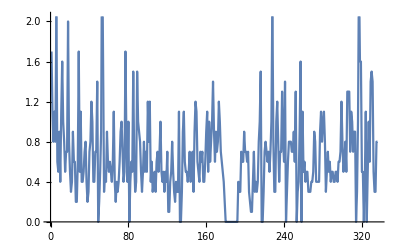

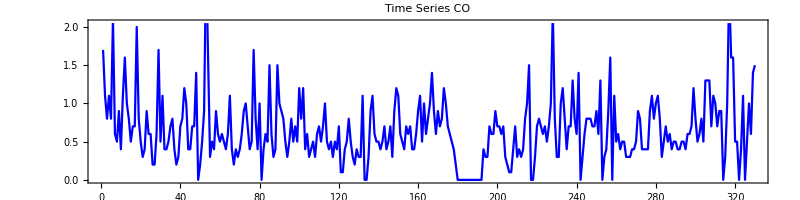

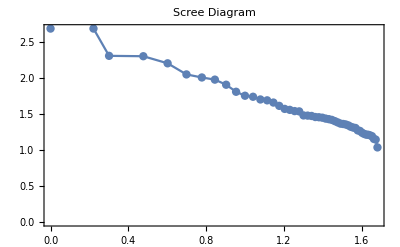

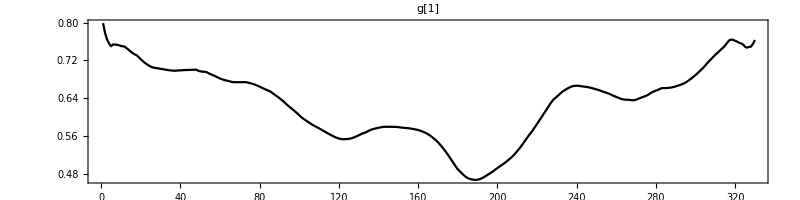

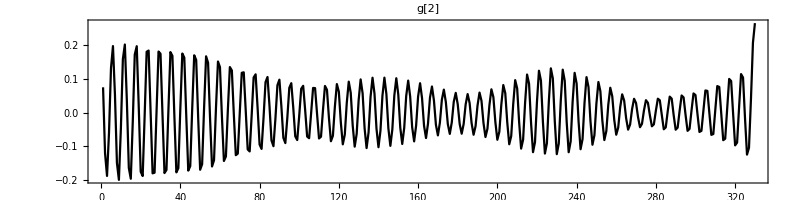

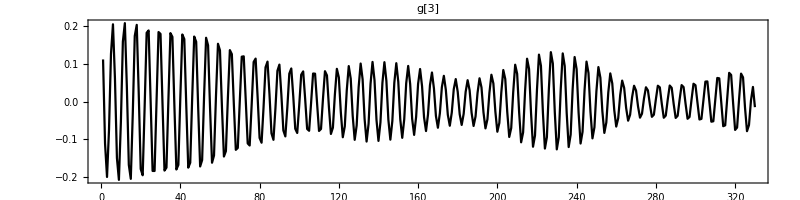

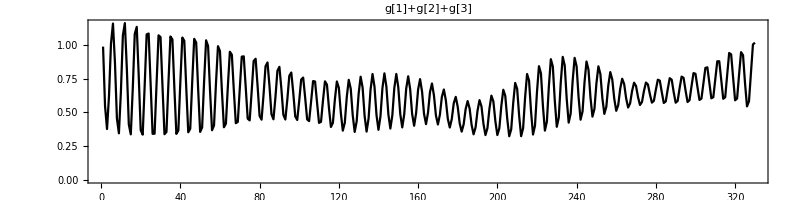

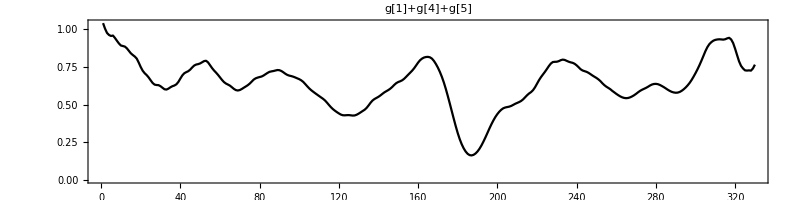

5

{1.22793,0.772212,0.587126,0.827574,1.21445,1.36146,1.05683,0.624095,0.498106,0.79271,1.20735,1.29606,0.952965,0.524925,0.438798,0.771097,1.16621,1.2065,0.821864,0.394766,0.340687,0.68849,1.05974,1.05392,0.666729,0.279054,0.269756,0.636282,0.995374,0.97675,0.60077,0.238686,0.253848,0.624275,0.9768,0.962697,0.604747,0.276361,0.31694,0.696403,1.04773,1.03775,0.693294,0.373726,0.410728,0.772388,1.10244,1.08141,0.738893,0.43113,0.472287,0.821404,1.12784,1.07759,0.72721,0.420118,0.441436,0.744046,1.00303,0.952383,0.637363,0.359964,0.37788,0.652556,0.898221,0.866857,0.593013,0.341604,0.348287,0.596509,0.840915,0.851892,0.631844,0.407765,0.406859,0.63469,0.875313,0.90226,0.705694,0.491343,0.468992,0.662859,0.883286,0.92239,0.756168,0.553683,0.521504,0.691021,0.892561,0.924402,0.759673,0.562722,0.521592,0.665353,0.840035,0.864731,0.713564,0.537487,0.509251,0.648695,0.803384,0.810795,0.651424,0.478274,0.45441,0.590633,0.733692,0.722961,0.559917,0.402225,0.403463,0.554452,0.687529,0.650713,0.467078,0.311627,0.33185,0.495854,0.621848,0.567612,0.376651,0.240245,0.297118,0.488197,0.616603,0.548469,0.35039,0.224979,0.305925,0.515877,0.648097,0.573637,0.372828,0.266012,0.375678,0.605232,0.736016,0.650088,0.448149,0.344344,0.451891,0.67103,0.789982,0.699172,0.501883,0.405902,0.515783,0.731774,0.846809,0.756329,0.563676,0.47192,0.579023,0.782961,0.88832,0.806099,0.636431,0.567087,0.680305,0.873631,0.968514,0.88877,0.731886,0.662058,0.750074,0.901834,0.960057,0.860291,0.694639,0.607872,0.656669,0.760782,0.783403,0.666431,0.487573,0.379602,0.397906,0.470589,0.474885,0.361699,0.202806,0.112328,0.143358,0.238301,0.284999,0.223101,0.101571,0.0356917,0.0952339,0.233065,0.32839,0.301454,0.19562,0.138632,0.216753,0.386445,0.509681,0.488726,0.363029,0.276066,0.339206,0.513424,0.641307,0.598265,0.426825,0.29819,0.350961,0.547126,0.699628,0.656668,0.458588,0.308747,0.372313,0.605416,0.789058,0.74648,0.523003,0.357952,0.436408,0.702338,0.910884,0.872083,0.642262,0.470588,0.549987,0.823526,1.03539,0.985237,0.728467,0.533952,0.601674,0.863223,1.05431,0.985539,0.731321,0.546015,0.606978,0.843074,1.00758,0.933984,0.692767,0.514601,0.567416,0.780521,0.929385,0.862899,0.649799,0.499816,0.54981,0.731803,0.850188,0.783127,0.592148,0.464224,0.508406,0.659279,0.75097,0.687539,0.537595,0.439484,0.473848,0.587581,0.658318,0.61634,0.508684,0.442278,0.477341,0.575962,0.645017,0.628918,0.555236,0.504498,0.532652,0.618879,0.68565,0.676653,0.609391,0.551821,0.56694,0.648622,0.71901,0.704926,0.610605,0.523497,0.526403,0.608627,0.681182,0.662652,0.565995,0.484247,0.497086,0.595059,0.685797,0.684577,0.599615,0.526869,0.553769,0.673694,0.789032,0.804182,0.727087,0.656174,0.691187,0.831812,0.973468,0.999598,0.900853,0.79497,0.808147,0.942835,1.07402,1.0716,0.928772,0.783894,0.793074,0.959122,1.11981,1.09735,0.900064,0.698082,0.670115,0.808592,0.945976,0.908345,0.69412,0.52226,0.560077,0.768783,0.986805,1.01708}

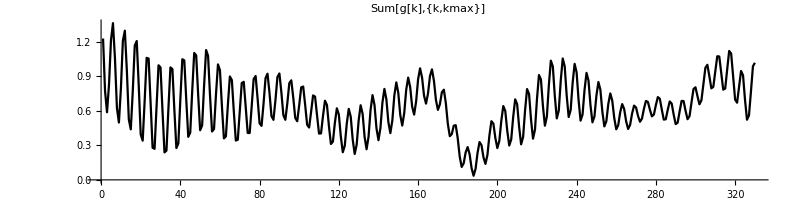

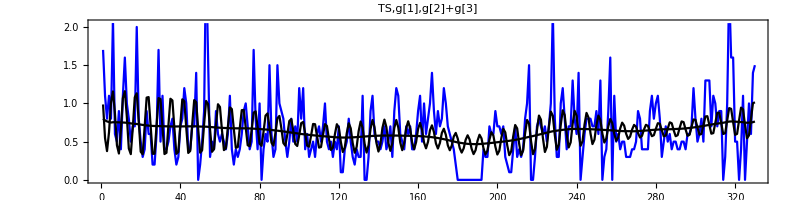

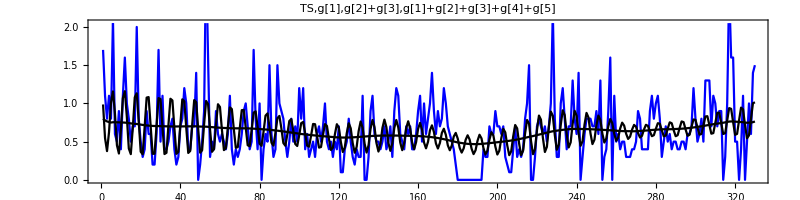

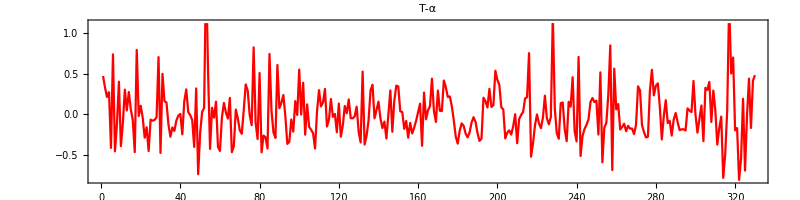

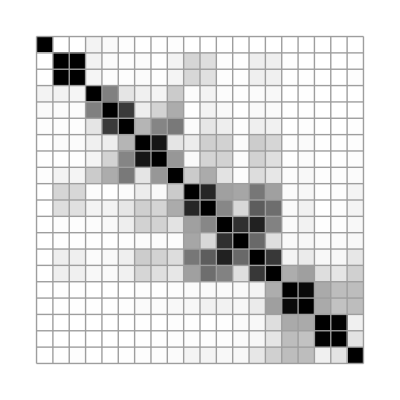

0.4720686597491952
0.3277883379633215
0.21287442864077344
0.27242609766862624
-0.4144509536729155
0.7385422440478036
-0.4568347188754892
-0.12409506055057817
0.4018935122259058
-0.3927101407775788
-0.10735048404871028
0.30394334119454625
0.04703466465266071
0.27507513692162733
0.06120204481398339
-0.07109714618347929
-0.4662123237762863
0.7935009547169556
-0.02186411613776995
0.10523401414519529
-0.04068668398790026
-0.2884896956415437
-0.15974497855334657
-0.4539232356492572
-0.06672888098293972
-0.07905411097750736
-0.06975563665739104
-0.03628219533015997
0.7046261183091369
-0.47675005076277865
0.4992301556532438
0.161313846630187
0.14615205222479732
-0.12427457189991409
-0.2768002663459248
-0.16269652105196764
-0.20474680515105093
-0.0763613494805464
-0.016940203657972053
0.003596876715727726
-0.24772815527748593
0.1622465617575657
0.3067059812081898
0.02627382814426238
-0.010728238527023926
-0.07238813150774492
-0.40243654847030963
0.31859446772626576
-0.7388925640848268
-0.23112996144321313
0.02771286126817568
0.0785955842350673
1.7721624854639564
0.5224125478456396
-0.42721026711402815
0.07988197419990267
-0.04143591398398416
0.15595385288747177
-0.4030316797269712
-0.45238336016143177
-0.03736286242851006
0.1400360560199005
0.02211983484448582
-0.05255646839717498
0.20177905843137134
-0.4668567724646683
-0.39301340314780137
0.05839603623351414
-0.04828717966339441
-0.19650857036425584
-0.24091450570078188
0.04810767676874261
0.3681563579274916
0.29223531869297725
-0.006859356099053859
-0.1346896378210254
0.824687056661912
-0.10225961687090479
-0.3056936889789207
0.508656703062537
-0.46899217165272744
-0.2628587040562893
-0.28328613662797353
-0.4223902264324345
0.7438319454080966
0.046316662274795584
-0.2215044005213878
-0.2910209353644183
0.6074390368516751
0.07559796392357343
0.14032689359823125
0.23727785633766652
-0.021592499412508293
-0.36535315546616615
-0.340035097353225
-0.06473065759684171
-0.2135640798199585
0.16251252822597584
-0.009251233547120652
0.5513054049967356
-0.0033842289739253184
0.38920458246996636
-0.2514243447968222
0.12172642462562894
-0.15441011632443996
-0.1906325029854108
-0.23369162033197322
-0.4229609191247426
0.04008274243836785
0.29777530823482024
0.09653720605113453
0.14554833564749425
0.3124710916334321
-0.1507126569846009
-0.06707778817219046
0.18837335546111023
-0.03185026023833598
0.004146439641392996
-0.22184806975881444
0.1323880229900677
-0.2766507116915352
-0.14024549993171956
0.1028818568384316
0.011803133561481993
0.18339745944294217
-0.04846940923927734
-0.05038972631756644
-0.02497918754923245
0.09407454150572564
-0.21587669873437393
-0.34809655553314595
0.5263625390487973
-0.37282771989677715
-0.266012368135889
-0.07567798979476159
0.2947681862837993
0.3639840732134165
-0.050087631919815134
0.05185096312431492
0.15565613655577837
-0.05189092821550978
-0.17103008369932216
-0.08998152356540645
-0.29917162120735086
-0.0018825373040847193
0.29409781096127763
-0.21578316437201056
0.16822562608564195
0.353191305631253
0.3436714356834587
0.036323522006504794
0.02808025912605705
-0.17902297319990068
-0.08296145197100269
-0.28832020623240806
-0.10609945397372489
-0.23643074380624174
-0.16708679234861357
-0.080305432385533
0.02636875642622305
0.13148554053628903
-0.3887696408759902
0.26811420752226045
-0.062057581133171724
0.04992648721706883
0.09816596935807143
0.4399433943857056
0.039708830601247636
-0.09463923394565177
0.2921281881165718
0.04333105365560597
0.03921783292219705
0.41659736416620574
0.3335688877133155
0.21242656956559347
0.22039761382714074
0.10209410801152918
-0.07058906366245515
-0.27488540623584024
-0.36169946980380885
-0.20280604237127703
-0.11232791964396704
-0.1433576857001465
-0.23830147123457024
-0.2849993117867604
-0.22310132649846098
-0.10157131837231026
-0.035691675686445434
-0.0952339076314952
-0.233064699366077
-0.32838977397509783
-0.3014540774559259
0.2043800468429613
0.16136757611183883
0.08324685631144435
0.3135550355415647
0.09031868013653932
0.11127436829013015
0.536970574649964
0.42393435306846405
0.36079364156500593
0.08657609582523429
0.05869304230197603
-0.29826544223634327
-0.22682539880199531
-0.19818989353288782
-0.2509605793182258
-0.14712587566729907
0.00037221638024398374
-0.35666790772555007
-0.0585875859855155
-0.008746802637212892
0.02768663374052216
0.19458447818235491
0.21094179016702752
0.7535200181289595
-0.5230029680950574
-0.35795182266899017
-0.13640757148447952
-0.0023376202037818095
-0.1108835949556064
-0.1720825719167619
-0.04226189767277766
0.22941209514277744
-0.049986562222183784
-0.1235258414962277
-0.03538929504763
1.2147625828621684
0.07153287978871803
-0.23395216286934312
-0.3016735389774751
0.1367768808616321
0.14568808187778792
-0.1855391673882112
-0.33132068210144017
0.1539853215191176
0.09302240072443668
0.4569255984562295
-0.20758425961093274
-0.33398423893228846
0.7072327439670949
-0.5146009568862104
-0.2674157992295823
-0.18052104660681845
-0.1293848281433303
-0.06289942037958995
0.15020120419025396
0.2001835421942429
0.15018996698155995
0.1681974840732664
-0.2501879682501693
0.5168726152298995
-0.59214761592493
-0.16422391442999823
-0.10840641905369586
0.24072105807352018
0.8490297723029129
-0.6875388455923005
0.5624048299389063
0.060516471555421336
0.1261515658654263
-0.18758118544218205
-0.15831789179990208
-0.11633964060144986
-0.2086838707677237
-0.1422783226169198
-0.17734076818845862
-0.17596153026534822
-0.24501686138374212
-0.12891808115532766
0.3447644895307632
0.2955015508333645
-0.13265201386611003
-0.21887870332322867
-0.2856497153667905
-0.27665292147726106
0.29060884916137175
0.5481785186934804
0.23306035801864966
0.3513777082833718
0.3809902560347872
0.09507357218244106
-0.31060536005940903
-0.023496557802413998
0.17359745829167805
-0.10862692000304253
-0.08118209588887715
-0.26265207598173423
-0.06599512454319667
0.015752794985146035
-0.09708632015577412
-0.1950592567974314
-0.18579746992206936
-0.18457676664135425
-0.1996145706363207
0.07313062275138826
0.04623117312471037
0.026306094633251176
0.4109681018347272
-0.004182295185703788
-0.22708672260220775
-0.056173650679188225
0.1088134293993046
-0.3318116597593893
0.3265317343140649
0.3004017630122513
0.39914678406790305
-0.09497003930319381
0.29185313491093967
0.05716475175769975
-0.3740150534335036
-0.1715985217492636
-0.028772301806327172
-0.783893660184082
-0.4930740031812099
0.0408775159611785
1.3801886022750973
0.502653327999153
0.6999356805892252
-0.19808202330232094
-0.17011466649184426
-0.8085915602040188
-0.5459762372428634
0.19165497028115297
-0.6941195129846334
-0.022260141874446804
0.43992284650921687
-0.168783334301276
0.41319462223787884
0.4829162693141478

```mathematica
Clear[U,Σ,V,r,σ,λ]
r=MatrixRank[Transpose[Datos]]
{U,Σ,V}=SingularValueDecomposition[N[Datos],r]

Clear[r,σ]
r=MatrixRank[Transpose[Datos]]
σ=SingularValueList[N[Transpose[Datos]],r]
λ=σ^2;
λLog=Table[{Log10[k],Log10[λ[[k]]]},{k,1,r}]

Serie=Flatten[Join[Table[Datos[[All,t]],{t,1,T}]]];

ListLinePlot[Serie]

L=48;
ScreeSSA[Serie,L];
FigSerie=ListLinePlot[Serie[[1;;330]],Frame -> True,PlotLabel->"Time Series CO",LabelStyle->Directive[Bold,Orange],PlotStyle->Blue,ImageSize->800,AspectRatio->1/4]

ListLinePlot[λLog,Mesh->All,Frame -> True,PlotLabel->"Scree Diagram",LabelStyle->Directive[Bold,Orange]]

CompleteSSA[Serie[[1;;330]],L];

Fig1=ListLinePlot[g[1],Frame -> True,PlotLabel->"g[1]",LabelStyle->Directive[Bold,Orange],PlotStyle->Black,ImageSize->800,AspectRatio->1/4]

Fig2=ListLinePlot[g[2],Frame -> True,PlotLabel->"g[2]",LabelStyle->Directive[Bold,Orange],PlotStyle->Black,ImageSize->800,AspectRatio->1/4]

Fig3=ListLinePlot[g[3],Frame -> True,PlotLabel->"g[3]",LabelStyle->Directive[Bold,Orange],PlotStyle->Black,ImageSize->800,AspectRatio->1/4]

Fig23=ListLinePlot[g[1]+g[2]+g[3],Frame -> True,PlotLabel->"g[1]+g[2]+g[3]",LabelStyle->Directive[Bold,Orange],PlotStyle->Black,ImageSize->800,AspectRatio->1/4]

Fig45=ListLinePlot[g[1]+g[4]+g[5],Frame -> True,PlotLabel->"g[1]+g[4]+g[5]",LabelStyle->Directive[Bold,Orange],PlotStyle->Black,ImageSize->800,AspectRatio->1/4]

kmax =5
alpha=Sum[g[k],{k,kmax}]

Figalpha=ListLinePlot[alpha,PlotLabel->"Sum[g[k],{k,kmax}]",LabelStyle->Directive[Bold,Orange],LabelStyle->Directive[Bold,Orange],PlotStyle->Black,ImageSize->800,AspectRatio->1/4]

Show[FigSerie,Fig1,Fig23,Frame -> True,PlotLabel->"TS,g[1],g[2]+g[3]",LabelStyle->Directive[Bold,Orange]]
Show[FigSerie,Fig1,Fig23,Fig12345,Frame -> True,PlotLabel->"TS,g[1],g[2]+g[3],g[1]+g[2]+g[3]+g[4]+g[5]",LabelStyle->Directive[Bold,Orange]]
Filtered = ListLinePlot[Serie[[1;;330]]-alpha,Frame -> True,PlotLabel->"T-α",LabelStyle->Directive[Bold,Orange],PlotStyle->Red,ImageSize->800,AspectRatio->1/4]

ArrayPlot[wMatriz,Mesh->All,Frame->All,FrameTicks->Automatic]

ExportString[Table[ Serie[[1;;330]]-alpha],"List"]
```